```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[σ1,SX2D+α*SX2DP]+KroneckerProduct[σ2,SY2D+α*SY2DP])+KroneckerProduct[σ3,m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP)]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,1.0,0.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

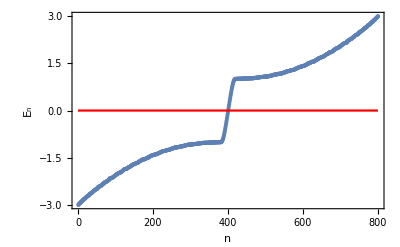

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
InvH=Inverse[HamiltonianQAHI[1.0,1.0,3.0,1.0]];
```

```mathematica
value=Eigenvalues[InvH];
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------- Computation of Bott Index -----------------*)
```

```mathematica
Clear[vecNormalized,ValVecNor,u,U,posx,POSX,posy,POSY,NmatX,NmatY,BottMatrix,BottEigenvalues,LogBottmat,LogBottMatrix]
```

```mathematica
vecNormalized=Table[Normalize[vec[[i]]],{i,1,2 A}];
```

```mathematica
ValVecNor=SortBy[Transpose[{val,vecNormalized}],First];
```

```mathematica
u[i_Integer,j_Integer]=0;

Do[
Do[
u[i,j]=
ValVecNor[[i,2,j]],
{i,1,A}
],
{j,1,2 *A}
]

U=Table[u[i,j],{i,A},{j,1,2*A}];
```

```mathematica
posx[i_Integer,j_Integer]=0;

Do[
Do[
posx[i+(j-1)Lx,i+(j-1)Lx]=Exp[I*π/Lx*(Mod[i,Lx,1])],
{i,1,2*A}
],
{j,1,2*A}
]

POSX=Table[posx[i,j],{i,1,2*A},{j,1,2*A}];

(*------------------------------------------------------------------*)

posy[i_Integer,j_Integer]=0;

Do[
Do[
posy[i+(j-1)Lx,i+(j-1)Lx]=Exp[I*π/Ly*(Mod[j,Ly,1])],
{i,1,2*A}
],
{j,1,2*A}
]

POSY=Table[posy[i,j],{i,1,2*A},{j,1,2*A}];
```

```mathematica
NmatX=U.POSX.ConjugateTranspose[U];
NmatY=U.POSY.ConjugateTranspose[U];
```

```mathematica
BottMatrix=NmatX.NmatY.ConjugateTranspose[NmatX].ConjugateTranspose[NmatX];
```

```mathematica
BottEigenvalues=Eigenvalues[BottMatrix];
```

```mathematica
LogBottmat[i_Integer,j_Integer]=0;

Do[
LogBottmat[i,i]=Log[BottEigenvalues[[i]]],
{i,1,A}
]

LogBottMatrix=Table[LogBottmat[i,j],{i,1,1*A},{j,1,1*A}];
```

```mathematica
Abs[Mod[Re[-I/(2*π)Tr[LogBottMatrix]],1]]//Chop
```

0

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites]
```

```mathematica
Sitelocation=Table[{i,j},{i,0,19},{j,0,19}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
Dimensions[FlatSite]
```

{800}

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,800,2}];
```

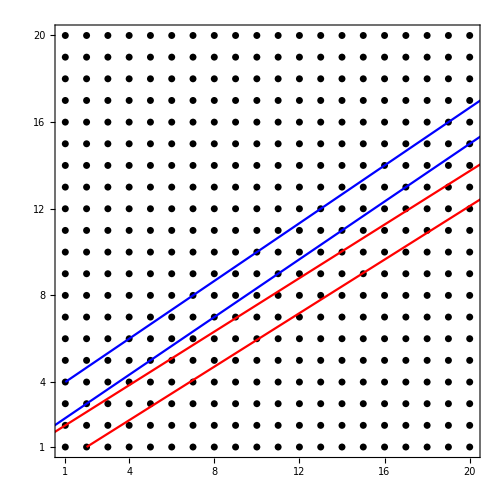

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{-0.1,19.1},{-0.1,19.1}}],
Plot[2/3*x+3,{x,0,20},PlotStyle-> Blue],Plot[2/3*x+4/3,{x,-1,20},PlotStyle-> Blue],
Plot[((1+√5)/2)^-1*x+1,{x,-1,20},PlotStyle-> Red],
Plot[((1+√5)/2)^-1*x-2/(1+√5),{x,1,20},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{0,"1"},{3,"4"},{7,"8"},{11,"12"},{15,"16"},{19,"20"}},None},{{{0,"1"},{3,"4"},{7,"8"},{11,"12"},{15,"16"},{19,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon]
```

```mathematica
Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};
```

```mathematica
Fibondown=Table[Fibonup[[j]]+400,{j,1,31}];
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
Dimensions[TotalFibon]
```

{62}

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
a=F1;
```

```mathematica
Do[
a=Drop[a,{TotalFibon[[62-i]]}],
{i,0,61,1}
]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,1.5,0.];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,62}
],
{j,1,62}
]
HFBFB=Table[Hfbfb[i,j],{i,1,62},{j,1,62}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,738}
],
{j,1,738}
]
H2D2D=Table[H2d2d[i,j],{i,1,738},{j,1,738}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,738}
],
{j,1,62}
]
H2DFB=Table[H2dfb[i,j],{i,1,738},{j,1,62}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,62}
],
{j,1,738}
]
HFB2D=Table[Hfb2d[i,j],{i,1,62},{j,1,738}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,62}]//Chop;
```

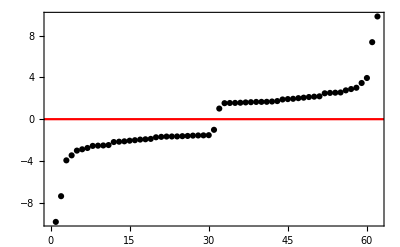

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black],Plot[0,{x,-100,100},PlotStyle-> Red]]
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,62}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

0

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[31+1,2]]
```

1.01674

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=31;
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[τ,ν,x,Fibon1D]
```

```mathematica
τ=(1+√5)/2;
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,31}]
```

{{1.,0},{1.85065,0},{2.37638,0},{3.22703,0},{3.75276,0},{4.60341,0},{5.45407,0},{5.9798,0},{6.83045,0},{7.6811,0},{8.20683,0},{9.05748,0},{9.58321,0},{10.4339,0},{11.2845,0},{11.8102,0},{12.6609,0},{13.5115,0},{14.0373,0},{14.8879,0},{15.4137,0},{16.2643,0},{17.115,0},{17.6407,0},{18.4913,0},{19.0171,0},{19.8677,0},{20.7184,0},{21.2441,0},{22.0948,0},{22.9454,0},{23.4711,0}}

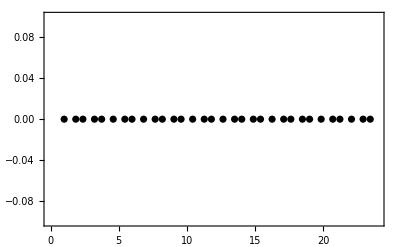

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,24},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,i]]]^2+Abs[ValVecFibon[[J,2,i+31]]]^2

+Abs[ValVecFibon[[J+1,2,i]]]^2+Abs[ValVecFibon[[J+1,2,i+31]]]^2

},{i,1,31}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]},{i,1,93,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibonacci[[All,3]];
```

```mathematica
rng[[2]]
```

0.606476

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.30"},{rng[[2]]-10^-3,"0.60"}}]
```

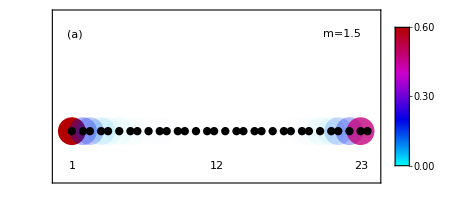

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,24.0},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[12,{12,-2.5}],Inset[23,{23,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

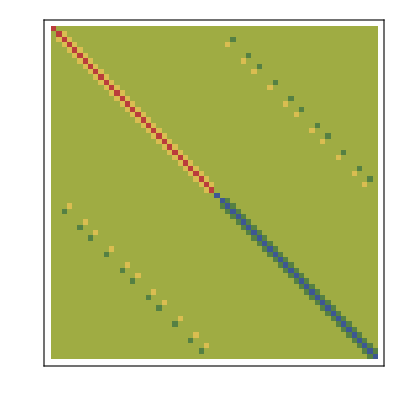

```mathematica
ArrayPlot[Re[HFBFB],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

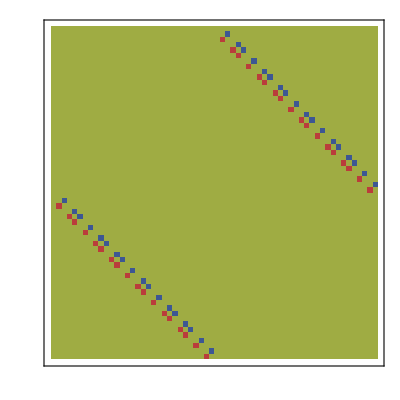

```mathematica
ArrayPlot[Im[HFBFB],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

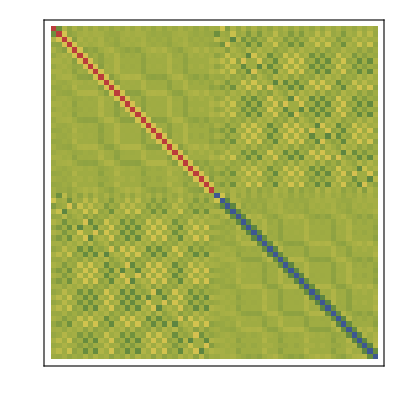

```mathematica
ArrayPlot[Re[HFibonRenor],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

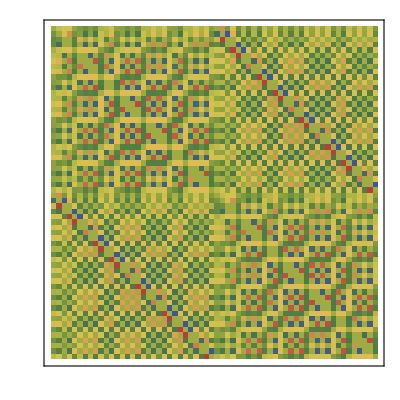

```mathematica
ArrayPlot[Im[HFibonRenor],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```